1. Naloga

```mathematica
d = Daljica[{-1,1},{3,-1}]
d2 = Daljica[{-1, -1}, {3, 1}]
d3 = Daljica[{-1, 2}, {3, 0}]
```

```mathematica
Dolzina[Daljica[AA_, BB_]] := Norm[BB -AA]
```

```mathematica
Dolzina[d]
```

2 √5

```mathematica
Slika[Daljica[AA_,BB_]] := Line[{AA, BB}]
```

```mathematica
Slika[d]
```

```mathematica
Narisi[d_Daljica] := Graphics[Slika[d]]
Narisi[d__Daljica] := Graphics[Map[Slika, List[d]]]
```

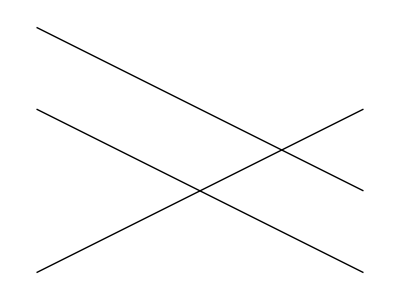

```mathematica
Narisi[d, d2, d3]
```

```mathematica
ClearAll[x, y]
EnacbaNosilke[Daljica[AA_,BB_]] := Module[{x1, y1, x2, y2, k, n},
{x1, y1}=AA;
{x2, y2}=BB;
k = (y2 - y1)/(x2 - x1);
n =n /.First[Solve[y1 == k*x1 + n, n]];
y ==  k*x + n
]
```

```mathematica
EnacbaNosilke[d]
```

y==1/2-x/2

2. Naloga

```mathematica
Presek[Daljica[AA_,BB_],Daljica[CC_,DD_]]:= Module[{resitev},
resitev = Solve[{AA + r(BB - AA) == CC + s(DD - CC), r ≥ 0, r ≤ 1, s ≥ 0, s ≤ 1}, {r, s}];
If[resitev == {},
{},
First[AA + r(BB - AA) /. resitev]
]
]
```

```mathematica
Presek[d, d2]
```

{1,0}

```mathematica
Presek[d, d3]
```

{}

3. Naloga

```mathematica
m1=Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]
m2 =Append[m1,m1[[1]]]
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2},{0,0}]

```mathematica
Slika[Mnogokotnik[t__]] := Line[{t}]
Slika[m2]
```

Line[{{0,0},{1,1},{0,3},{-1,2},{0,0}}]

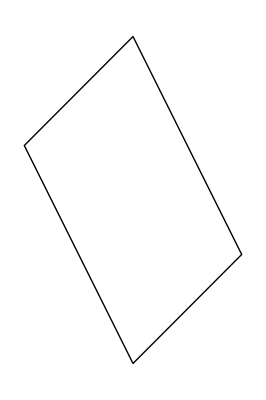

```mathematica
Narisi[m__Mnogokotnik] := Graphics[Slika[m]]
Narisi[m2]
```

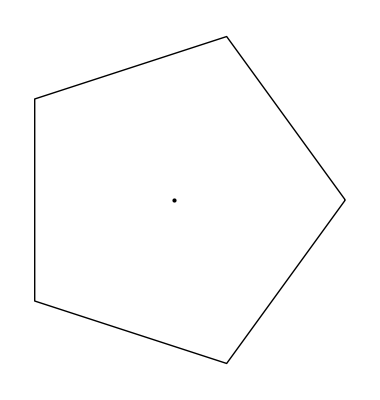

```mathematica
PravilniNKotnik[n_,r_] :=Graphics[{Line[Table[{r*Cos[(2Pi*i)/n],r*Sin[(2Pi*i)/n]},{i,0,n}]],Point[{0,0}]}]
p5 = PravilniNKotnik[5,2]
```

```mathematica
PravilniNKotnik2[n_,r_] := Show[Graphics[{{EdgeForm[Thick],White,RegularPolygon[{0,0},r,n]},{Point[{0,0}]}}]]
p55=PravilniNKotnik2[5,2]
```

-Graphics-

```mathematica
PravilniNKotnik[n_,r_,phi_] := Graphics[{Line[Table[{r*Cos[(2Pi*i+phi)/n ],r*Sin[(2Pi*i+phi)/n]},{i,0,n}]],Point[{0,0}]}]
Manipulate[PravilniNKotnik[5,2,phi],{phi,1.57,32.99}]
```

```mathematica
Daljice[Mnogokotnik[t__]] := Map[Daljica,Partition[{t}, 2,1]]
daljice = Daljice[m2]
```

{Daljica[{{0,0},{1,1}}],Daljica[{{1,1},{0,3}}],Daljica[{{0,3},{-1,2}}],Daljica[{{-1,2},{0,0}}]}

```mathematica
Partition[{1,2,3,4,5},2]
Partition[{1,2,3,4,5},2,1]
```

{{1,2},{3,4}}

{{1,2},{2,3},{3,4},{4,5}}

4. Naloga
(ni rešena)

```mathematica
Presek2[m_Mnogokotnik,d_Daljica] := Presek[daljice[[1]],d]
Presek2[m2,d]
daljice[[1]]
```

Presek[Daljica[{{0,0},{1,1}}],Daljica[{-1,1},{3,-1}]]

Daljica[{{0,0},{1,1}}]

```mathematica
Presek[d,Slika[d2]]
```

Presek[Daljica[{-1,1},{3,-1}],Line[{{-1,-1},{3,1}}]]

5. Naloga
(potrebujem dobro razlago)

```mathematica
ClearAll[f, a, b, d]
```

```mathematica
VsiPari[f_, sez1_, sez2_]:= Flatten[Outer[f, sez1, sez2], 1]
```

```mathematica
VsiPari[f, {1, 2,3 },{a, b}]
```

{f[1,a],f[1,b],f[2,a],f[2,b],f[3,a],f[3,b]}

```mathematica
q= Outer[f, {1, 2,3 },{a, b}]
```

{{f[1,a],f[1,b]},{f[2,a],f[2,b]},{f[3,a],f[3,b]}}

```mathematica
Flatten[q]
```

{f[1,a],f[1,b],f[2,a],f[2,b],f[3,a],f[3,b]}

```mathematica
Flatten[{{b, 2},{1, 3, {4}},{f, {g, h}}}]
```

{b,2,1,3,4,f,g,h}

```mathematica
Flatten[{{b, 2},{1, 3, {4}},{f, {g, h}}}, 1]
```

{b,2,1,3,{4},f,{g,h}}

```mathematica
Flatten[{{b, 2},{1, 3, {4}},{f, {g, h}}}, 2]
```

{b,2,1,3,4,f,g,h}

```mathematica
Outer[{b, 2},{1, 3, {4}},{f, {g, h}}]
```

{{{b,2}[1,f],{{b,2}[1,g],{b,2}[1,h]}},{{b,2}[3,f],{{b,2}[3,g],{b,2}[3,h]}},{{{b,2}[4,f],{{b,2}[4,g],{b,2}[4,h]}}}}

```mathematica
Outer[f,{a,b},{x,y,z}]
```

{{f[a,x],f[a,y],f[a,z]},{f[b,x],f[b,y],f[b,z]}}

```mathematica
m2 = Mnogokotnik[{0,0},{1,1},{0,3},{-1, 2}]
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]

```mathematica
m3 = Mnogokotnik[{0,1},{1,2},{2,3},{-5, 2}]
```

Mnogokotnik[{0,1},{1,2},{2,3},{-5,2}]

```mathematica
Presek[m1_Mnogokotnik, m2_Mnogokotnik]:= VsiPari[f, m1, m2]
```

```mathematica
Presek[m1, m2]
Presek[m1, m3]
```

Mnogokotnik[f[{0,0},{0,0}],f[{0,0},{1,1}],f[{0,0},{0,3}],f[{0,0},{-1,2}],f[{1,1},{0,0}],f[{1,1},{1,1}],f[{1,1},{0,3}],f[{1,1},{-1,2}],f[{0,3},{0,0}],f[{0,3},{1,1}],f[{0,3},{0,3}],f[{0,3},{-1,2}],f[{-1,2},{0,0}],f[{-1,2},{1,1}],f[{-1,2},{0,3}],f[{-1,2},{-1,2}]]

Mnogokotnik[f[{0,0},{0,1}],f[{0,0},{1,2}],f[{0,0},{2,3}],f[{0,0},{-5,2}],f[{1,1},{0,1}],f[{1,1},{1,2}],f[{1,1},{2,3}],f[{1,1},{-5,2}],f[{0,3},{0,1}],f[{0,3},{1,2}],f[{0,3},{2,3}],f[{0,3},{-5,2}],f[{-1,2},{0,1}],f[{-1,2},{1,2}],f[{-1,2},{2,3}],f[{-1,2},{-5,2}]]

6. Naloga
Nariši ABCD deltoid, ter poišči komponente točke D.

```mathematica
AA = {-5, 6, -4}
BB = {-4, -1, 2}
CC = {-1, -2, 4}
```

{-5,6,-4}

{-4,-1,2}

{-1,-2,4}

Najti je treba komponente točke D. Pri čemer potrebujemo vektor AS(projekcija AB na AC). Vektor AS se dobi z enačbo:

```mathematica
(AC . AB)/(AC)^2* AC
```

```mathematica
AB = BB - AA
AC = CC - AA
```

{1,-7,6}

{4,-8,8}

```mathematica
AS = Dot[AC, AB]/Dot[AC, AC]* AC
```

{3,-6,6}

Potrebno je dodati točko 0, ki ima komponente {0, 0, 0}, da tako pridemo do točke D preko vetkorja OD.

```mathematica
OA = AA
BA = -AB
OO = {0, 0, 0}
```

{-5,6,-4}

{-1,7,-6}

{0,0,0}

```mathematica
OD = OA + AS + BA + AS
```

{0,1,2}

```mathematica
DD = OD - OO
```

{0,1,2}

Tako smo prišli do točke D  s komponentami {0, 1, 2}.

```mathematica
Deltoid = {{AA}, {BB}, {CC}, {DD}}
```

{{{-5,6,-4}},{{-4,-1,2}},{{-1,-2,4}},{{0,1,2}}}

```mathematica
Stranice[{AA_,BB_,CC_, DD_}] :={{AA, BB}, {BB, CC}, {CC, DD}, {DD, AA}}
SlikaOglisc[Deltoid_] := Map[Point, Deltoid]
SlikaStranic[Deltoid_] := Map[Line, Stranice[Deltoid]]
```

```mathematica
NarisiDeltoid[Deltoid_]:= Graphics3D[{
Blue,PointSize[0.02],Thickness[0.005],
SlikaOglisc[Deltoid], 
Line[{AA, BB}], Line[{BB, CC}], Line[{CC, DD}], Line[{DD,AA}],
Black, Dashed, Line[{AA, CC}], Line[{BB, DD}],
Red,PointSize[0.02], Point[{(BB + DD)/2}]
}]
```

```mathematica
NarisiDeltoid[Deltoid]
```

-Graphics3D-